```mathematica
hlow[x_]:=0.231166897578547+0.19579947200452*x-0.00147163230560322*x^2;
dlow[x_] := hlow'[x];
hmid[x_]:=-22.4033436605957+1.25361724755983*x-0.0183301586082401*x^2+0.000138923728362529*x^3-5.16376654974849*^-7*x^4+7.53834532810923*^-10*x^5;
dmid[x_]:=hmid'[x];
hup[x_]:=104.127497960411-0.708174149227273*x+0.00163976643013219*x^2;
dup[x_]:=hup'[x];
a = Sqrt[19]/9;
b = Sqrt[12.2]/5.6;
c = Sqrt[15.93]/6.35;
w1= 10.5;
w2 =2;
l = 60;
vmax = 277;
hmax = hup[vmax];
k1 = 2*Sqrt[1+a^2] + Sqrt[1+b^2] + Sqrt[1+c^2];
k2 = 2*a+b+c;
k3 = w1+w2;
calow[x_]:=2*(k1*Sqrt[2*hmax*hlow[x]-hlow[x]^2]+k2*hlow[x]+k3)*dlow[x];
camid[x_]:=2*(2*Sqrt[2*hmax*hmid[x]-hmid[x]^2]+l*hmax/Sqrt[2*hmax*hmid[x]-hmid[x]^2])*dmid[x];
caup[x_]:=2*(k1*Sqrt[2*hmax*hup[x]-hup[x]^2]+k2*(hmax - hup[x])+k3)*dup[x];
```

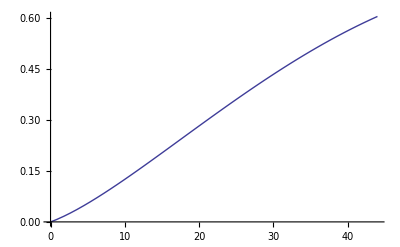

```mathematica
Plot[NIntegrate[calow[x],{x,0,y}]*0.0254^2,{y,0,44}]
```

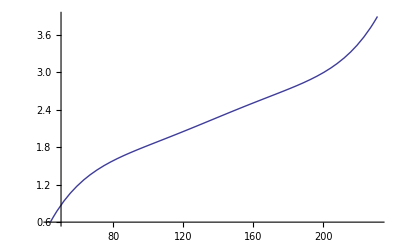

```mathematica
a1 = NIntegrate[calow[x],{x,0,44}];
Plot[(NIntegrate[camid[x],{x,44,y}]+a1)*0.0254^2,{y,44,231}]
```

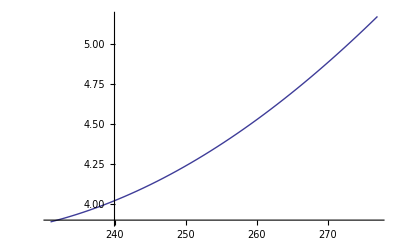

```mathematica
a2 = a1 + NIntegrate[camid[x],{x,44,231}];
Plot[(NIntegrate[caup[x],{x,231,y}]+a2)*0.0254^2,{y,231,277}]
```

```mathematica
Export["calow.txt",Table[{y,NIntegrate[calow[x],{x,0,y}]},{y,0,44,0.1}],"Table"]
Export["camid.txt",Table[{y,NIntegrate[camid[x],{x,44,y}]+a1},{y,44,231,0.1}],"Table"]
Export["caup.txt",Table[{y,NIntegrate[caup[x], {x,231,y}]+a2},{y,231,277,0.1}],"Table"]
```

calow.txt

camid.txt

caup.txt